# Least Squares Fitting

### Author

Eric W. Weisstein
January 19, 2012

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Statistics/LeastSquaresFitting.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/LeastSquaresFitting.html.

©2011 Wolfram Research, Inc. except for portions noted otherwise

### Notes

This is some of Eric's very old code.  It should be rewritten and cleaned up.

### Code

```mathematica
PolynomialData[a_List,n_,noise_:0]:=Module[
{
x=Table[Random[],{n}],
y,
i,k
},y=Table[noise Random[Real,{-1,1}]+Sum[a[[k]] x[[i]]^(k-1),{k,Length[a]}],{i,n}];
{x,y}
]

PolynomialFit[x_List,y_List,n_]:=Module[
{X,i,k},X=Table[Table[x[[i]]^(k-1),{k,n}],{i,Length[x]}];
LinearSolve[Transpose[X].X,Transpose[X].y]
]

Cor[x_List,y_List]:=Module[{
n=Length[y],
xsum=Plus@@x,
ysum=Plus@@y,
xx=x.x,xy=x.y,yy=y.y
},
(n xy-xsum ysum)^2/(n xx-xsum^2)/(n yy-ysum^2)
]

Options[PolynomialFitPlot]={
LineStyle->{},
PointStyle->{}
};

PolynomialFitPlotV5[a0_List,n_,noise_,opts___]:=Module[
{
d=PolynomialData[a0,n,noise],
a,
i,cor,minx,maxx,miny,maxy,
linestyle=PlotStyle->LineStyle/.{opts}/.Options[PolynomialFitPlot],
pointstyle=PlotStyle->PointStyle/.{opts}/.Options[PolynomialFitPlot],
graphopts=FilterOptions[Graphics,opts]
},
{minx,maxx}=Through[{Min,Max}[d[[1]]]];
{miny,maxy}=Through[{Min,Max}[d[[2]]]];
a=PolynomialFit[d[[1]],d[[2]],Length[a0]];
cor=Cor@@d;
Message[PolynomialFit::info,a,cor];
Show[
{
ListPlot[Transpose[d],
pointstyle,
PlotLabel->TraditionalForm[r==cor],
DisplayFunction->Identity
],
Plot[a[[1]]+Sum[a[[i+1]] x^i,{i,Length[a0]-1}],{x,0,1},
DisplayFunction->Identity,
Evaluate[linestyle]
]
},
graphopts,
DisplayFunction->$DisplayFunction
  ] 
]


PolynomialFitPlot[a0_List,n_,noise_,opts___]:=Module[
{
d=PolynomialData[a0,n,noise],
a,
i,cor,minx,maxx,miny,maxy,
linestyle=PlotStyle->LineStyle/.{opts}/.Options[PolynomialFitPlot],
pointstyle=PlotStyle->PointStyle/.{opts}/.Options[PolynomialFitPlot],
graphopts=Sequence@@FilterRules[{opts},Options@Graphics]
},
{minx,maxx}=Through[{Min,Max}[d[[1]]]];
{miny,maxy}=Through[{Min,Max}[d[[2]]]];
a=PolynomialFit[d[[1]],d[[2]],Length[a0]];
cor=Cor@@d;
Message[PolynomialFit::info,a,cor];
Show[
{
ListPlot[Transpose[d],
pointstyle,
PlotLabel->r==cor
],
Plot[a[[1]]+Sum[a[[i+1]] x^i,{i,Length[a0]-1}],{x,0,1},
Evaluate[linestyle]
]
},
graphopts
  ] 
]


PolynomialFit::info="Fit parameters `1` with correlation r^2=`2`";

LinearFit[x_List,y_List]:=Module[{n=Length[y],xsum=Plus@@x,ysum=Plus@@y,xx=x.x,xy=x.y,a,b},b=(xy-xsum ysum/n)/(xx-xsum^2/n);
a=(ysum-b xsum)/n;
{a,b}]
```

## Linear and Quadratic

```mathematica
Show[GraphicsArray[{
PolynomialFitPlot[{1,2},100,.2,
DisplayFunction->Identity,
LineStyle->Red,
PlotRange->{Automatic,{-.1,3}}
],
PolynomialFitPlot[{1,2,-5},100,.2,
LineStyle->Red,
DisplayFunction->Identity]
}
],DisplayFunction->$DisplayFunction]
```

PolynomialFit::info: Fit parameters {0.997174, 2.01185} with correlation r^2=0.960733

PolynomialFit::info: Fit parameters {0.990797, 2.04976, -5.03448} with correlation r^2=0.822805

⁃GraphicsArray⁃

## Linear Fit as a Function of Noise

#### V5

```mathematica
Off[General::"stop"];
Show[GraphicsArray[Partition[PolynomialFitPlot[{1,2},100,#,
PlotRange->{-.5,5.1},
PointStyle->PointSize[.02],
LineStyle->Red,
DisplayFunction->Identity]&/@{0,.1,.3,.5,1,2},3]]]
```

PolynomialFit::info: Fit parameters {1., 2.} with correlation r^2=1.

PolynomialFit::info: Fit parameters {1.0117, 1.97608} with correlation r^2=0.989981

PolynomialFit::info: Fit parameters {1.00226, 1.97431} with correlation r^2=0.923884

PolynomialFit::info: Fit parameters {0.964239, 1.91688} with correlation r^2=0.758385

PolynomialFit::info: Fit parameters {1.1227, 1.87829} with correlation r^2=0.44648

PolynomialFit::info: Fit parameters {0.915192, 2.3278} with correlation r^2=0.260971

⁃GraphicsArray⁃

#### V6

PolynomialFit::info: Fit parameters {1., 2.} with correlation r^2=1.

PolynomialFit::info: Fit parameters {0.973148, 2.03385} with correlation r^2=0.988727

PolynomialFit::info: Fit parameters {1.01204, 2.00764} with correlation r^2=0.911891

PolynomialFit::info: Fit parameters {0.990099, 2.0265} with correlation r^2=0.803293

PolynomialFit::info: Fit parameters {0.844491, 2.31975} with correlation r^2=0.581112

PolynomialFit::info: Fit parameters {0.859657, 2.22006} with correlation r^2=0.219453

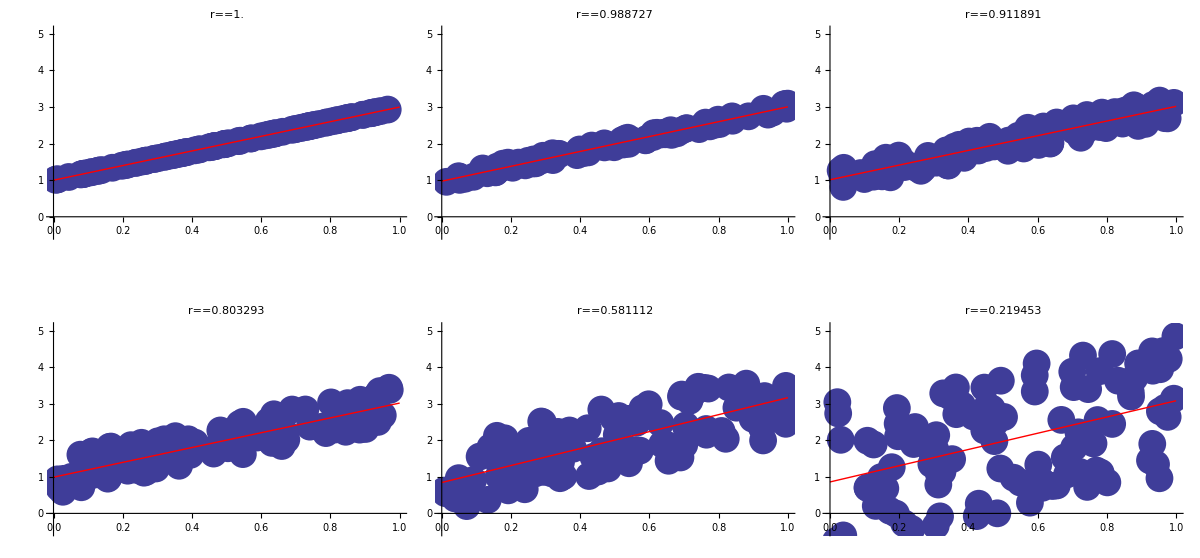

```mathematica
GraphicsGrid[Partition[PolynomialFitPlot[{1,2},100,#,
PlotRange->{-.5,5.1},
PointStyle->PointSize[.05],
LineStyle->Red]&/@{0,.1,.3,.5,1,2},3],Spacings->{-30,30}]
```